```mathematica
Needs["NDSolve`FEM`"]
```

# Circular integration test with better boundaries

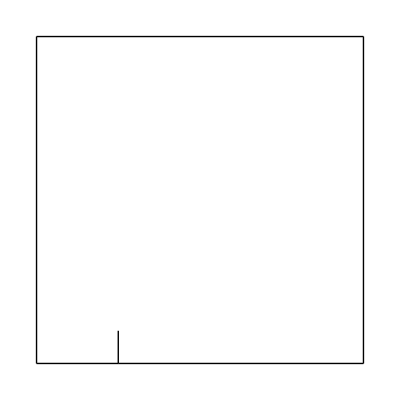

```mathematica
boundary = ToBoundaryMesh[
"Coordinates"->{
{0,0},
{0.25,0},
{0.25,0.1},
{1,0},
{1,1},
{0,1}
},
"BoundaryElements"->{
LineElement[{
{1,2},
{2,3},
{2,4},
{4,5},
{5,6},
{6,1}},
{2,2,2,2,2,2}
]
}
];
reg = ToElementMesh[boundary,
"MeshQualityGoal"->0.7, 
"MaxCellMeasure"->{"Area"->0.01},
MeshRefinementFunction->Function[{vertices,area},(area ≥0.00001Norm[{0.25,0.1}-Mean[vertices]])]
];
boundary["Wireframe"]
```

```mathematica
sol=NDSolveValue[
{
Laplacian[u[x,y],{x,y}]+1==0,
{DirichletCondition[u[x,y]==0,x≤0||x≥1||y≤0||y≥0],
DirichletCondition[u[x,y]==0,x==0.25&&y≥0&&y≤0.1]}
},
u,
{x,y}∈reg,
AccuracyGoal->25,PrecisionGoal->25];
```

```mathematica
Show[
ContourPlot[sol[x,y],{x,y}∈reg],
Graphics[{
Red, Circle[{0.25,0.1},0.1], 
White, Point[{0.25,0.1}]}]
]
```

-Graphics-

#### Now we will integrate in circle

```mathematica
DiskIntegr=NIntegrate[sol[x,y],{x,y}∈Disk[{0.25,0.1},0.1],AccuracyGoal->20,PrecisionGoal->15, MaxRecursion->45]//Quiet
RealDigits[DiskIntegr]
```

0.000461138

{{4,6,1,1,3,8,2,3,4,4,4,6,5,3,6,3},-3}

Value evaluated from FreeFem++ is 0.000461324 relative difference is 0.04%.

```mathematica
(0.000461324 - 0.0004611382344465363)/0.000461324 * 100
```

0.0402679

```mathematica
NIntegrate[sol[x,y],{x,y}∈Disk[{0.25,0.1},0.01],AccuracyGoal->20,PrecisionGoal->15, MaxRecursion->45]//Quiet
```

1.62911×10^-6

RealDigits[DiskIntegr]

#### Whole region

```mathematica
wholeRigIntegr=NIntegrate[sol[x,y],{x,y}∈reg,AccuracyGoal->20,PrecisionGoal->7,MaxRecursion->45]
RealDigits[wholeRigIntegr]
```

0.034202

{{3,4,2,0,2,0,2,3,6,0,8,5,7,1,0,2},-1}

Value evaluated from FreeFem++ is 0.034202 relative difference is 0.00005%!!!

```mathematica
0.0000000202360857102/0.03420202360857102*100
```

0.0000591663

#### Max Value of function

```mathematica
maxval=NMaxValue[sol[x,y],{x,y}∈reg]//Quiet;
RealDigits[maxval]
Print[maxval]
```

{{7,2,5,7,9,2,1,8,3,4,6,0,3,5,5,1},-1}

0.0725792

# Test With exact implementation like in FreeFem++

```mathematica
BaseVector[nf_Integer, zf_]:=If[Mod[nf,2]==0,-Im[zf^(nf/2.)],Re[zf^(nf/2.)]]
```

```mathematica
BaseVector[3,2I]
```

-2.

```mathematica
BaseVector[1,1]
```

1.

```mathematica
BaseVector[1,2]
```

1.41421

```mathematica
BaseVector[2,1]
```

0

```mathematica
BaseVector[2, I]
```

-1.

```mathematica
BaseVector[3,1]
```

1.

```mathematica
BaseVector[3,2I]
```

-2.

```mathematica
Sqrt[3]/2//N
```

0.866025

### predefined integral

```mathematica
R = 0.01(*same radius is in freefem*);
exponant = 2(*value from FreeFem*);
tipangle = Pi/2;
x0 = 0.25;
y0 = 0.1;

a[order_Integer]:=
NIntegrate[
sol[x,y] 
Exp[-((√((x - 0.25)^2+(y - 0.1)^2))/R)^exponant]
BaseVector[order, 
Exp[-I tipangle] (x-x0 + I(y - y0)) 
],
{x,y}∈Disk[{x0,y0},3R],
AccuracyGoal->20, 
PrecisionGoal->7,
MaxRecursion->50,
WorkingPrecision->16]/
NIntegrate[
Exp[-((√((x - 0.25)^2+(y - 0.1)^2))/R)^exponant]
BaseVector[order, 
Exp[-I tipangle] (x-x0 + I(y - y0)) ]^2,
{x,y}∈Disk[{x0,y0},3R],
AccuracyGoal->20, 
PrecisionGoal->7,
MaxRecursion->50,
WorkingPrecision->16]
```

### And final value check!

```mathematica
a[1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.102110587511622

```mathematica
a[2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.8871472970103464717692747871728417304598631667630513929703929134×10^-10 and 2.12036174630272643855848654755380635564827673908302454983934608102×10^-16 for the integral and error estimates.

0.0454658719778866

```mathematica
a[3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.88361627959472893279644492349467208608360714258887268063907147418×10^-12 and 1.60094472597134021258894435477084883424247481129329272768335405106×10^-17 for the integral and error estimates.

0.123287949871927

#### Now lets compare these series params with what are from FreeFem

```mathematica
(0.102110587511622424669761935715423-0.101866)/0.101866*100
```

0.240107

0.2% of difference for a1

```mathematica
(0.0454658719778 - 0.0454618)/0.0454618*100
```

0.00895692

0.008% of difference for a2

```mathematica
(-0.1232879498719 + 0.13087)/0.1232879498719 *100
```

6.14987

6 % of difference for a3

# From Simpler Formula without BaseVector

### TODO later.. ask Piotr Szymczak about this problem..

# MeshRefinmentFunction

```mathematica
SingleTip[r_, exp_, maxarea_,r0_]:=(1+maxarea-Exp[-(r/r0)^exp]);
```

```mathematica
tipPoints = {{0,0},{1,1},{0.5,1}};
```

```mathematica
Manipulate[
Plot3D[
Min@Map[
SingleTip[Norm[{x,y}-#],exp[[1]],0.0001,exp[[2]]]&, 
{p1,p2,p3}],
{x,0,1},{y,0,1},
PlotRange->All,
PerformanceGoal->"Quality",
PlotTheme->"ZMesh",
PlotPoints->{100,100}],
{exp,{0,0.01},{10,1}},
{p1,{0,0},{1,1}},
{p2,{0,0},{1,1}},
{p3,{0,0},{1,1}},ControlType->Slider2D
]
```

## Angle of New Point evaluation Test 30.03

```mathematica
0.0233587,0.0117224
```

```mathematica
-ArcTan[2*0.0117224/0.0233587 √0.01]//RealDigits
```

{{1,0,0,0,3,3,5,8,8,9,3,8,7,1,7,7},0}

```mathematica
Cos[-0.03184168030963936]*0.01
```

0.00999493

```mathematica
Sin[-0.03184168030963936]*0.01
```

-0.000318363

BUT C++ gives -1.4767824476518645 not -0.0318416803!!!! Strange!

```mathematica
-1.4767824476518645
```

0.0940139

```mathematica
Pi/2//N
```

1.5708

```mathematica
ArcTan@-1.4767824476518645
```

-0.975573

```mathematica
ArcTan[√3]
```

π/3

#### What wrong with this?? Polar Model::next_point(vector<double> series_params) { //FIXME: should here be - or +???? double phi = -atan(2 * series_params[2]/series_params[1] * sqrt(ds)); return {ds, phi}; }

#### Indexes was wrong :)

# Import Json

```mathematica
Dialog[]
```

```mathematica
SystemDialogInput["FileOpen"]
```

/home/oleg/Dev/riversim/build/simulation_data.json

```mathematica
res=Import[SystemDialogInput["FileOpen"]]
```

{Border→{SomeDetails→points and lines should be in counterclockwise order!,SourceIndexes→{{1,4}},coords→{{1.,0.},{1.,30.},{0.,30.},{0.,0.},{0.75,0.}},lines→{{0,1,1},{1,2,2},{2,3,3},{3,4,4},{4,0,4}}},Description→This is RiverSim simulation data,Model→{Integration→{exponant→4.,radius→0.1},Mesh→{eps→1/1000000,exponant→4.,max-area→0.1,min-angle→30.,min-area→1/10000000,refinment-radius→0.3},biffurcation-angle→0.628319,biffurcation-threshold→-100.,biffurcation-type→0,boundary-condition→1,boundary-ids→{1,2,3,4},ds→0.01,dx→0.75,eta→0.,field-value→0.,growth-threshold→0,growth-type→0,height→30.,river-boundary-id→4,width→1.},RuntimeInfo→{EachCycleTime→{5.45855×10^9,8.12653×10^9,1.08929×10^10,1.36087×10^10,1.66601×10^10,1.9468×10^10,2.23127×10^10,2.57463×10^10,2.93228×10^10,3.23633×10^10,3.55597×10^10,3.88145×10^10,4.24984×10^10,4.58766×10^10,4.90731×10^10,5.15619×10^10,5.41706×10^10,5.6677×10^10},EndDate→Fri Apr 12 03:37:51 2019
,InputFile→TODO,StartDate→Fri Apr 12 03:36:55 2019
,TotalTime→5.58192×10^11},Trees→{Branches→{{coords→{{0.75,0.},{0.749625,0.00999296},{0.750277,0.0199716},{0.750444,0.0299703},{0.750755,0.0399654},{0.750846,0.049965},{0.750779,0.0599648},{0.75103,0.0699616},{0.751461,0.0799523},{0.751479,0.0899523},{0.751203,0.0999485},{0.751124,0.109948},{0.75103,0.119948},{0.751019,0.129948},{0.750967,0.139948},{0.751089,0.149947},{0.751047,0.159947},{0.751054,0.169947},{0.751086,0.179947},{0.751145,0.189947},{0.751083,0.199946},{0.751108,0.209946},{0.750958,0.219945},{0.75083,0.229944},{0.750417,0.239936},{0.750102,0.249931},{0.749651,0.259921},{0.749185,0.26991},{0.748968,0.279907},{0.748713,0.289904},{0.748358,0.299898},{0.747835,0.309884},{0.747432,0.319876},{0.7468,0.329856},{0.74629,0.339843},{0.745791,0.349831},{0.745208,0.359814},{0.744708,0.369801},{0.743852,0.379764},{0.743261,0.389747},{0.742362,0.399706},{0.741137,0.409631},{0.73993,0.419558},{0.738958,0.429511},{0.737602,0.439418},{0.736245,0.449326},{0.734998,0.459248},{0.733598,0.469149},{0.732131,0.479041},{0.730696,0.488938},{0.729273,0.498836},{0.727786,0.508725},{0.72628,0.518611},{0.724692,0.528484},{0.723169,0.538367},{0.721674,0.548255},{0.720036,0.55812},{0.718755,0.568037},{0.717285,0.577928},{0.716078,0.587855},{0.714891,0.597785},{0.713594,0.6077},{0.712191,0.617601},{0.710913,0.627519},{0.709886,0.637467},{0.708899,0.647418},{0.707655,0.65734},{0.706568,0.667281},{0.705581,0.677232},{0.704171,0.687132},{0.702574,0.697004},{0.700825,0.706849},{0.698966,0.716675},{0.697007,0.726481},{0.695045,0.736287},{0.693436,0.746157},{0.691727,0.75601},{0.690183,0.76589},{0.688686,0.775777},{0.687027,0.785638},{0.685506,0.795522},{0.683957,0.805401},{0.682495,0.815294},{0.681145,0.825202},{0.679891,0.835124},{0.678637,0.845045},{0.677532,0.854983},{0.676488,0.864929},{0.675371,0.874866},{0.674091,0.884784},{0.672783,0.894698},{0.6716,0.904628},{0.670274,0.914539},{0.668995,0.924457},{0.667817,0.934388},{0.666518,0.944303},{0.665061,0.954196},{0.663705,0.964104},{0.662331,0.974009},{0.661012,0.983922},{0.65946,0.993801},{0.657747,1.00365},{0.656293,1.01355},{0.654878,1.02345},{0.653306,1.03332},{0.651573,1.04317},{0.649699,1.05299},{0.647902,1.06283},{0.646128,1.07267},{0.644557,1.08255},{0.642791,1.09239},{0.641167,1.10226},{0.639518,1.11212},{0.6378,1.12197},{0.636219,1.13185},{0.634833,1.14175},{0.633501,1.15166},{0.632244,1.16158},{0.630727,1.17147},{0.629312,1.18136},{0.627846,1.19126},{0.626419,1.20115},{0.625076,1.21106},{0.62384,1.22099},{0.622599,1.23091},{0.621463,1.24085},{0.620242,1.25077},{0.618779,1.26066},{0.617679,1.2706},{0.616077,1.28047},{0.614584,1.29036},{0.613056,1.30024},{0.611628,1.31014},{0.61034,1.32006},{0.608871,1.32995},{0.607417,1.33984},{0.606045,1.34975},{0.604773,1.35967},{0.603778,1.36962},{0.60272,1.37956},{0.601888,1.38953},{0.600952,1.39948},{0.599891,1.40943},{0.598623,1.41935},{0.597394,1.42927},{0.59607,1.43918},{0.594837,1.44911},{0.593498,1.45902},{0.592404,1.46896},{0.591374,1.4789},{0.590273,1.48884},{0.589206,1.49878},{0.58836,1.50875},{0.587248,1.51869},{0.586129,1.52862},{0.585135,1.53857},{0.584199,1.54853},{0.583238,1.55848},{0.582379,1.56845},{0.581393,1.5784},{0.580193,1.58833},{0.578815,1.59823},{0.577274,1.60811},{0.575547,1.61796},{0.574147,1.62786},{0.572324,1.63769},{0.571025,1.64761},{0.569797,1.65753},{0.568614,1.66746},{0.567639,1.67742},{0.566722,1.68737},{0.565756,1.69733},{0.564568,1.70726},{0.563496,1.7172},{0.562728,1.72717},{0.561983,1.73714},{0.5609,1.74708},{0.560108,1.75705},{0.559476,1.76703},{0.558691,1.777},{0.558102,1.78698},{0.557786,1.79698},{0.557401,1.80697},{0.557162,1.81697},{0.557185,1.82697},{0.557143,1.83697},{0.556837,1.84696},{0.5564,1.85695},{0.555837,1.86694},{0.555342,1.87693},{0.55491,1.88692},{0.554177,1.89689},{0.553594,1.90687},{0.552998,1.91685},{0.552392,1.92684},{0.551817,1.93682}},id→1,source_angle→1.5708,source_point→{0.75,0.}}},Relations→{},SourceIds→{1}}}

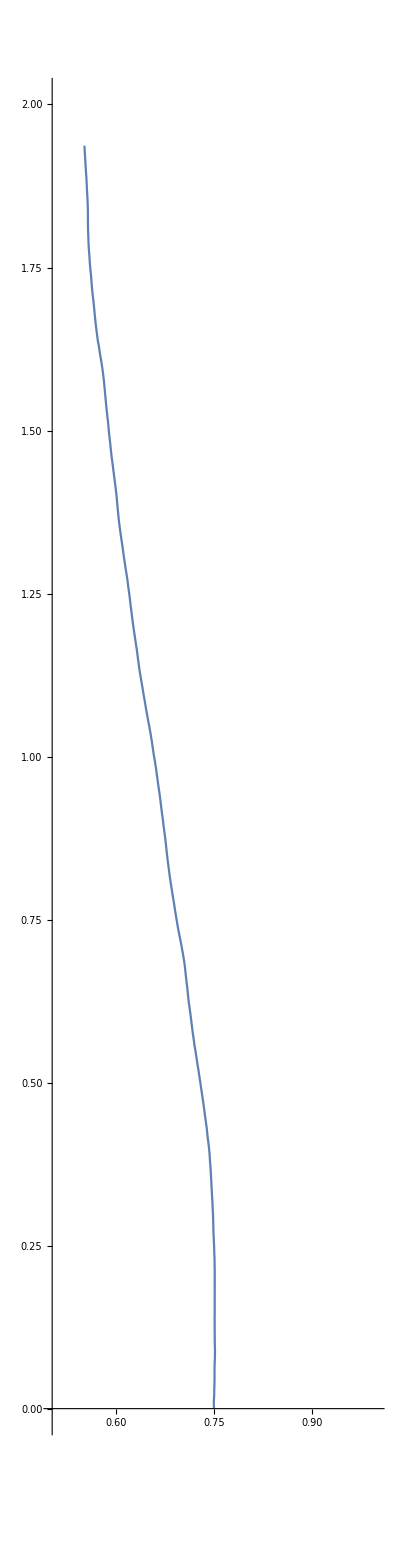

```mathematica
ListPlot[res[[5,2,1,2,1,1,2]],Joined->True,PlotRange->{{0.5,1},{0,2}},AspectRatio->4]
```